```mathematica
SetDirectory[NotebookDirectory[]];
Get["../sources/KimberlingTrilinears1000.m"]; 
Get["../sources/TriangleExpressions.m"]; 
Get["../sources/KimberlingPoints.m"];
```

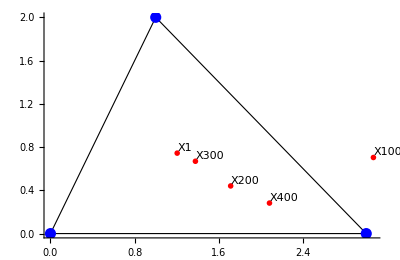

{{(3 (1+√5))/(3+2 √2+√5),6/(3+2 √2+√5)},{(3+8 √2-√5-4 √10)/(2+2 √2+2 √5-3 √10),((-3+2 √2) (-3+√5))/(-2-2 √2-2 √5+3 √10)},{(2+8 √2-4 √5-4 √10)/(1+√2+√5-3 √10),(-3+2 √2+√5)^2/(-2-2 √2-2 √5+6 √10)},{(4 (9 √10 (-1+√3)+5 Sec[1/6 (π-6 ArcCos[1/(√10)])]))/(12 √10 (-1+√3)+15 √2 Sec[1/6 (π-6 ArcCos[1/(√5)])]+20 Sec[1/6 (π-6 ArcCos[1/(√10)])]),(40 Sec[1/6 (π-6 ArcCos[1/(√10)])])/(12 √10 (-1+√3)+15 √2 Sec[1/6 (π-6 ArcCos[1/(√5)])]+20 Sec[1/6 (π-6 ArcCos[1/(√10)])])},{(3 (√5 Csc[π/16]^4+Csc[1/4 ArcCos[1/(√10)]]^4))/(√5 Csc[π/16]^4+2 √2 Csc[1/4 ArcCos[1/(√5)]]^4+3 Csc[1/4 ArcCos[1/(√10)]]^4),(6 Csc[1/4 ArcCos[1/(√10)]]^4)/(√5 Csc[π/16]^4+2 √2 Csc[1/4 ArcCos[1/(√5)]]^4+3 Csc[1/4 ArcCos[1/(√10)]]^4)}}

```mathematica
PA={0,0}; PB={3,0}; PC={1,2};
indices = {1,100,200, 300, 400};
centers =Table[KimberlingCenter[i,PA,PB,PC],{i,indices}]//Simplify;
names=Table["X"<>TextString[n],{n,indices}];
Graphics[Join[
{EdgeForm[{Thin, Black}], FaceForm[], Triangle[{PA,PB,PC}]},
{{PA, PB, PC}/.{x_,y_}:>{Blue,PointSize[0.02],Point[{x,y}]}},
{centers/.{x_,y_}:>{Red,PointSize[0.01],Point[{x,y}]}},
Text[#[[1]],#[[2]],-1.5 Sign@#[[2]]]&/@Transpose@{names, centers}
], AspectRatio->Automatic, Axes-> True
]
centers
```